# Actividad 1

## Wei Le Hu Tang

Instrucciones: Para  los  siguientes  modelos  definir  el  Lagrangiano  y  calcular  las  ecuaciones de  Euler - Lagrange. Graficar  la  variación  de  la  posición  y  velocidad  con  respecto  del  tiempo, así  como  el  retrato  fase  de  ambos  sistemas . Verificar  si  los  modelos  son  análogos  o  no . Proponer  una  situación  donde  ustedes  propondrían  utilizar  un  modelo  como  el  de  la  figura 1.

El Lagrangiano se define como  donde  es la energía cinética y  la energía potencial.

Donde
(T=1/2(masa)(velocidad))^2
Como la velocidad es la tasa de cambio de posición, entonces velocidad=x'
1/2 m (x')^2
Esto en ambos casos

Por otro lado
U=1/2(coeficiente de elasticidad)(distancia deformada)^2
Hay dos resortes con coeficientes k_1 y k_2
En el primer caso se deforman en sentidos contrarios
U=1/2 k_1 x^2+1/2(k_2(-x))^2=1/2 k_1 x^2+1/2 k_2 x^2
-Graphics-
En el segundo caso se deforman en el mismo sentido
U=1/2 k_1 x^2+1/2 k_2 x^2
-Graphics-
Tal que en ambos casos:
U=1/2 x^2(k_1+k_2)

Entonces el Lagrangiano, para las dos figuras es:
L=T-U=1/2 m (x')^2-1/2 x^2(k_1+k_2)

Con el cual obtendremos la ecuación de Euler-Lagrange:
(∂L)/(∂x)-d/dt(∂L)/(∂x')=0
(∂L)/(∂x)=-x(k_1+k_2)
(∂L)/(∂x')=m x'
d/dt(∂L)/(∂x')=m x''

Como k_1 y k_2 son dos constantes positivas, sea k=k_1+k_2
Entonces:
-x k-m x''=0
m x''=-x k
x''=-x k/m

Con esto ya podemos graficar la velocidad y la posición respecto al tiempo usando Mathematica

```mathematica
sol = With[{k=2,m=3}, (*definios constantes*)
	DSolve[{x''[t]==-k/m * x[t], (*la ecuación diferencial de segundo grado*)
		x'[0]==0,x[0]==5}, x, t]]; (*condiciones iniciales*)
x[t] /. sol
x'[t] /. sol

Plot[{x[t] /. sol, x'[t] /. sol}, {t,0,25}, (*gráficas*)
	PlotLabels->{"Posición","Velocidad"}, (*etiquetas*)
	PlotRange->Full]
```

DSolve::deqn: Equation or list of equations expected instead of True in the first argument {True,True,True}.

ReplaceAll::reps: {DSolve[{True,True,True},x,t]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

x[t]/.DSolve[{True,True,True},x,t]

ReplaceAll::reps: {DSolve[{True,True,True},x,t]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

x'[t]/.DSolve[{True,True,True},x,t]

DSolve::dsvar: 0.000510714 cannot be used as a variable.

ReplaceAll::reps: {DSolve[{True,True,True},x,0.000510714]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

DSolve::dsvar: 0.510715 cannot be used as a variable.

ReplaceAll::reps: {DSolve[{True,True,True},x,0.510715]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

DSolve::dsvar: 1.02092 cannot be used as a variable.

General::stop: Further output of DSolve::dsvar will be suppressed during this calculation.

ReplaceAll::reps: {DSolve[{True,True,True},x,1.02092]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-Graphics-

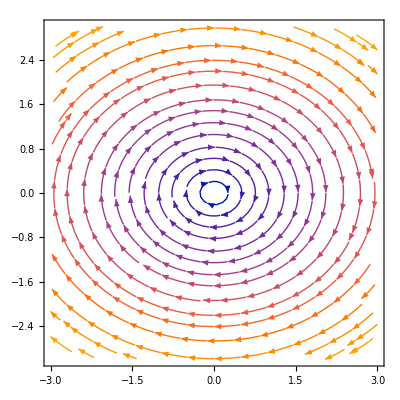

```mathematica
(*definiremos las constantes*)
k=2;
m=3;
(*se definen dos funciones*)
f[x_,y_]:=y; (*posición*)
h[x_,y_]:=-k/m*x; (*velocidad, ya que es x'' la derivada de la velocidad*)
StreamPlot[{f[x,y],h[x,y]}, (*con estas dos funciones se definen la dirección y el sentido de las flechas*)
	{x,-3,3},{y,-3,3}, (*rangos de las x,y*)
	Axes->True]
```